```mathematica
g=Import["/home/justanotherlad/Documents/BTech Degree Project/Facebook datas/socfb-CMU.txt"];
```

```mathematica
g1=ToExpression[StringSplit[g]]
```

{143,1,545,1,582,1,850,1,1071,1,3144,1,3182,1,3649,1,3738,1,4119,1,4276,1,4557,1,5264,1,5376,1,5478,1,5767,1,6581,1,199,2,278,2,309,2,430,2,433,2,462,2,464,2,499,2,570,2,665,2,800,2,927,2,1037,2,499798,6574,6572,6580,6572,6587,6572,6593,6572,6584,6575,6592,6575,6587,6576,6589,6576,6590,6576,6618,6576,6598,6578,6582,6581,6589,6581,6593,6581,6589,6582,6593,6582,6605,6582,6588,6584,6589,6584,6596,6585,6601,6585,6590,6588,6616,6588,6593,6589,6616,6590,6618,6593,6613,6595,6616,6602,6615,6604,6611,6609}
 |  |  |  |

```mathematica
g2=DeleteCases[Flatten[Table[UndirectedEdge[i,j]&&i≠j,{i,0,Max[g1]},{j,i+1,Max[g1]}]],False];
```

```mathematica
g3=DeleteDuplicates[ReplacePart[g1,Table[{{i},{i+1}}->UndirectedEdge[g1[[i+1]],g1[[i]]],{i,1,Length@g1,2}]]]
```

{1<->143,1<->545,1<->582,1<->850,1<->1071,1<->3144,1<->3182,1<->3649,1<->3738,1<->4119,1<->4276,1<->4557,1<->5264,1<->5376,1<->5478,1<->5767,1<->6581,2<->199,2<->278,2<->309,2<->430,2<->433,2<->462,2<->464,2<->499,2<->570,2<->665,2<->800,2<->927,249901,6572<->6580,6572<->6587,6572<->6593,6575<->6584,6575<->6592,6576<->6587,6576<->6589,6576<->6590,6576<->6618,6578<->6598,6581<->6582,6581<->6589,6581<->6593,6582<->6589,6582<->6593,6582<->6605,6584<->6588,6584<->6589,6585<->6596,6585<->6601,6588<->6590,6588<->6616,6589<->6593,6590<->6616,6593<->6618,6595<->6613,6602<->6616,6604<->6615,6609<->6611}
 |  |  |  |

```mathematica
intersectpos=With[{disp=Dispatch[Thread[g3->"foo"]]},Flatten@Position[Replace[g2,disp,{1}],"foo"]];
```

```mathematica
g2=ReplacePart[g2,Table[intersectpos[[i]]->DirectedEdge[g2[[intersectpos[[i]],1]],g2[[intersectpos[[i]],2]]],{i,Length[intersectpos]}]];
```

```mathematica
MonochromaticCliqueTester[n_,e_,x_]:=Module[{subedges,newEdges,graph,i,j,var,coloredSubgraphs,cliques,list={{},{}}},


For[i=0,i<Floor@N@(Max[g1]/1000),i++,
subedges=Select[g2,(1000*i<#[[1]]<1000*(i+1))&&(1000*i<#[[2]]<1000*(i+1))&];
newEdges=Replace[subedges,{DirectedEdge[a_,b_]:>Style[UndirectedEdge[a,b],Red],UndirectedEdge[a_,b_]:> Style[UndirectedEdge[a,b],Blue]},{1}];
graph=Graph[newEdges];

For[j=1,j<=x,j++,

var=Subgraph[graph,{RandomInteger[{1000*i,1000*(i+1)},e]}];
coloredSubgraphs=Quiet[GroupBy[MapAt[Lookup[LineColor],AnnotationValue[var,EdgeStyle],{All,2}],Last->First]];
cliques=Length@First@FindClique[#]≥n&/@coloredSubgraphs;
AppendTo[list[[1]],cliques[[1]]];
If[Length@cliques>1,AppendTo[list[[2]],cliques[[2]]]];
]
];


Labeled[BarChart[{{Length@Cases[list[[1]],True],Length@Cases[list[[2]],True]}},ChartBaseStyle->EdgeForm[Dashed],ChartStyle->{Blue,Red},ChartLegends->{"Don't Know Each Other in Facebook","Know Each Other in Facebook"},BarSpacing->None,ChartLabels->{{"Clique Exists"},{"Blue Cliques","Red Cliques"}},LabelingFunction->(Placed[Row[{#,"/",N[x*i]}],Above]&),PlotLabel->Style["Finding " <>ToString[n]<>"-Cliques in a Complete "<>ToString[e]<>"-Graph","Title",16],ImageSize->Medium,PerformanceGoal->"Speed"],Column[{"Probability that there are "<>ToString[n]<>" people knowing each other in a party of "<>ToString[e]<>" at CMU is roughly "<>ToString[N[Length@Cases[list[[2]],True]/N[x*i]]],"Probability that there are "<>ToString[n]<>" people not knowing each other in a party of "<>ToString[e]<>" at CMU is roughly "<>ToString[N[Length@Cases[list[[1]],True]/N[x*i]]]}],LabelStyle->Directive[FontSize->13.5,FontFamily->"Times"]]
] (*Gives a bar chart of how many times monochromatic n-cliques of colors blue and red were found resp. in a complete graph of e vertices (taken randomly from the entire imported social-media graph in batches of successive 1000 vertices at a time till all the vertices are taken into consideration) when the experiment is run a total of x times*)
```

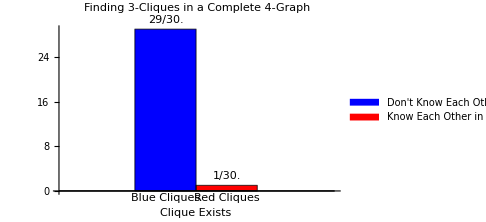
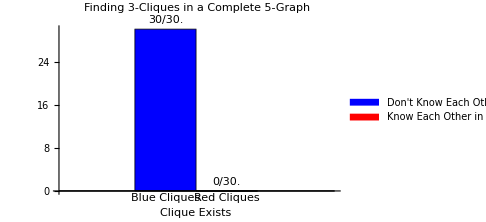
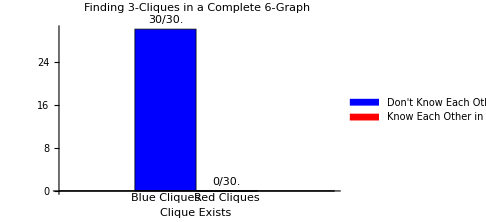
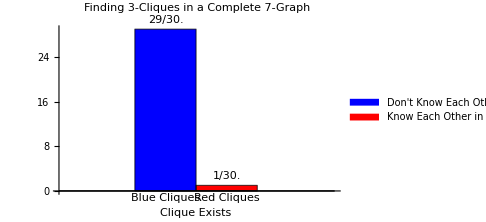
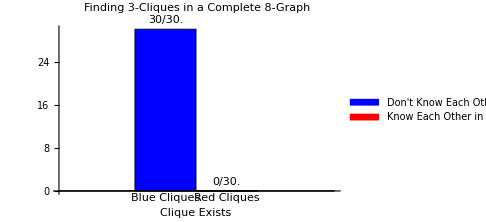
{-Graphics-Probability that there are 3 people knowing each other in a party of 4 at CMU is roughly 0.0333333
Probability that there are 3 people not knowing each other in a party of 4 at CMU is roughly 0.966667,-Graphics-Probability that there are 3 people knowing each other in a party of 5 at CMU is roughly 0.
Probability that there are 3 people not knowing each other in a party of 5 at CMU is roughly 1.,-Graphics-Probability that there are 3 people knowing each other in a party of 6 at CMU is roughly 0.
Probability that there are 3 people not knowing each other in a party of 6 at CMU is roughly 1.,-Graphics-Probability that there are 3 people knowing each other in a party of 7 at CMU is roughly 0.0333333
Probability that there are 3 people not knowing each other in a party of 7 at CMU is roughly 0.966667,-Graphics-Probability that there are 3 people knowing each other in a party of 8 at CMU is roughly 0.
Probability that there are 3 people not knowing each other in a party of 8 at CMU is roughly 1.}

```mathematica
MonochromaticCliqueTester[3,#,5]&/@{4,5,6,7,8}
```